## These plots are generated in BC_CumulativeBeta.nb

## BrownAn00

```mathematica
Print[DateSequence[DateList[],"yes"]];
MatrixNote[Tmat]
Print[" UforNM1 = ", MatrixForm[UforNM1]];
```

12-26-2023 18:36

T is BrownAn00

UforNM1 = (0.921451 | -0.368714 | -0.12239
-0.365504 | -0.929543 | 0.0485472
-0.131666 | 0. | -0.991294)

#### List all angles for all node sequences and all node modes

```mathematica
nodeSequences={ΣnTETXISO,ΣnTETCUBE,ΣnTRIGXISO,ΣnTRIGCUBE};
nodeModes={nm1,nm2,nm3};
results=Flatten[Table[{DisplayAngles[nodeSeq,nodeMode],"\n\n"},
{nodeSeq,nodeSequences},{nodeMode,nodeModes}],1];
StringJoin[results]//Print
```

node sequence is ΣnTETXISO, node mode is nm1
TRIV-MONO     6.76    TRIV..MONO     6.76
MONO-ORTH    12.91    TRIV..ORTH    19.67
 ORTH-TET    11.69     TRIV..TET    31.36
 TET-XISO     1.11    TRIV..XISO    32.47
 XISO-ISO    18.54     TRIV..ISO    51.00

node sequence is ΣnTETXISO, node mode is nm2
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-ORTH     5.22    TRIV..ORTH     8.99
 ORTH-TET     4.82     TRIV..TET    13.81
 TET-XISO    17.92    TRIV..XISO    31.74
 XISO-ISO    18.54     TRIV..ISO    50.27

node sequence is ΣnTETXISO, node mode is nm3
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-ORTH     5.21    TRIV..ORTH     8.98
 ORTH-TET     4.69     TRIV..TET    13.67
 TET-XISO    17.69    TRIV..XISO    31.36
 XISO-ISO    17.77     TRIV..ISO    49.14

node sequence is ΣnTETCUBE, node mode is nm1
TRIV-MONO     6.76    TRIV..MONO     6.76
MONO-ORTH    12.91    TRIV..ORTH    19.67
 ORTH-TET    11.69     TRIV..TET    31.36
 TET-CUBE    13.70    TRIV..CUBE    45.06
 CUBE-ISO    12.66     TRIV..ISO    57.72

node sequence is ΣnTETCUBE, node mode is nm2
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-ORTH     5.22    TRIV..ORTH     8.99
 ORTH-TET     4.82     TRIV..TET    13.81
 TET-CUBE    19.76    TRIV..CUBE    33.57
 CUBE-ISO    15.59     TRIV..ISO    49.16

node sequence is ΣnTETCUBE, node mode is nm3
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-ORTH     5.21    TRIV..ORTH     8.98
 ORTH-TET     4.69     TRIV..TET    13.67
 TET-CUBE    19.72    TRIV..CUBE    33.40
 CUBE-ISO    15.47     TRIV..ISO    48.87

node sequence is ΣnTRIGXISO, node mode is nm1
TRIV-MONO     6.76    TRIV..MONO     6.76
MONO-TRIG    17.55    TRIV..TRIG    24.30
TRIG-XISO     2.41    TRIV..XISO    26.72
 XISO-ISO    18.54     TRIV..ISO    45.25

node sequence is ΣnTRIGXISO, node mode is nm2
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-TRIG    16.47    TRIV..TRIG    20.24
TRIG-XISO    20.68    TRIV..XISO    40.92
 XISO-ISO    18.54     TRIV..ISO    59.46

node sequence is ΣnTRIGXISO, node mode is nm3
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-TRIG    16.13    TRIV..TRIG    19.90
TRIG-XISO    12.95    TRIV..XISO    32.85
 XISO-ISO    15.88     TRIV..ISO    48.73

node sequence is ΣnTRIGCUBE, node mode is nm1
TRIV-MONO     6.76    TRIV..MONO     6.76
MONO-TRIG    17.55    TRIV..TRIG    24.30
TRIG-CUBE    13.19    TRIV..CUBE    37.50
 CUBE-ISO    12.66     TRIV..ISO    50.16

node sequence is ΣnTRIGCUBE, node mode is nm2
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-TRIG    16.47    TRIV..TRIG    20.24
TRIG-CUBE    22.40    TRIV..CUBE    42.65
 CUBE-ISO    15.59     TRIV..ISO    58.24

node sequence is ΣnTRIGCUBE, node mode is nm3
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-TRIG    16.13    TRIV..TRIG    19.90
TRIG-CUBE    15.57    TRIV..CUBE    35.47
 CUBE-ISO    13.33     TRIV..ISO    48.80

#### Sequentially add nm1, nm2, nm3 to each plot

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### direct, nm1, nm2, nm3 for four different node sequences

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## BrownAn25

#### Sequentially add nm1, nm2, nm3 to each plot

12-7-2023 5:32

T is BrownAn25

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.983909 | -0.154509 | -0.0897222
-0.153871 | -0.987991 | 0.0140314
-0.0908127 | 0. | -0.995868)

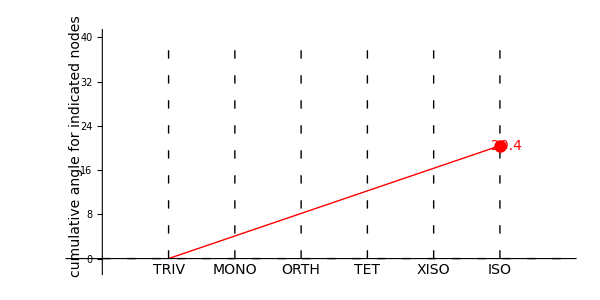

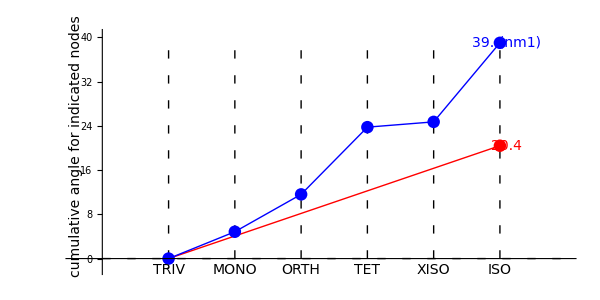

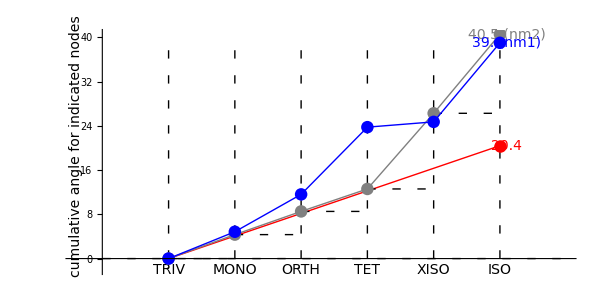

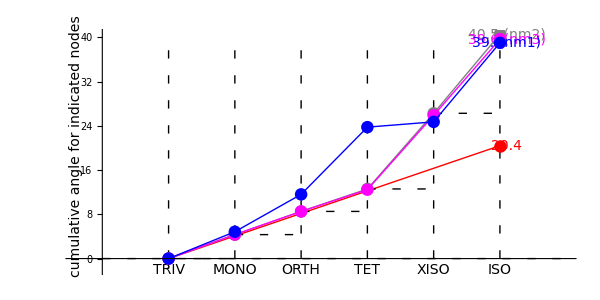

#### direct, nm1, nm2, nm3 for four different node sequences

-Graphics-

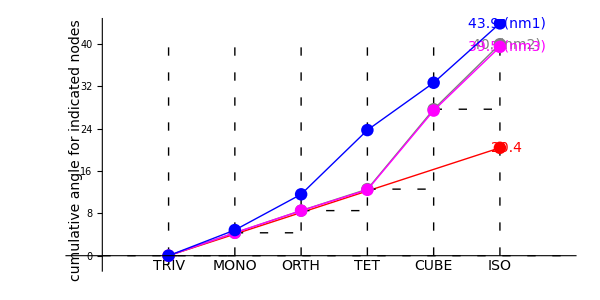

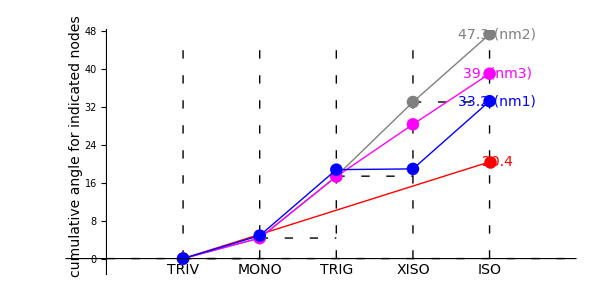

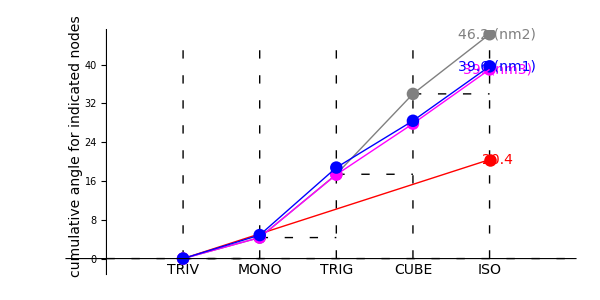

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

## BrownAn37

#### Sequentially add nm1, nm2, nm3 to each plot

12-7-2023 5:54

T is BrownAn37

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.0025682 | -0.99849 | -0.0548752
-0.0466789 | -0.0549353 | 0.997398
-0.998907 | 0. | -0.0467495)

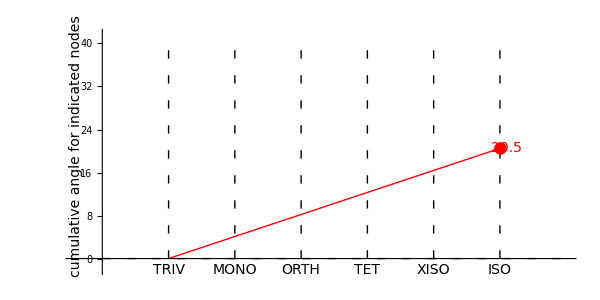

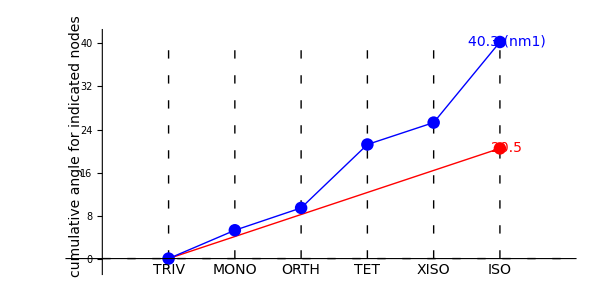

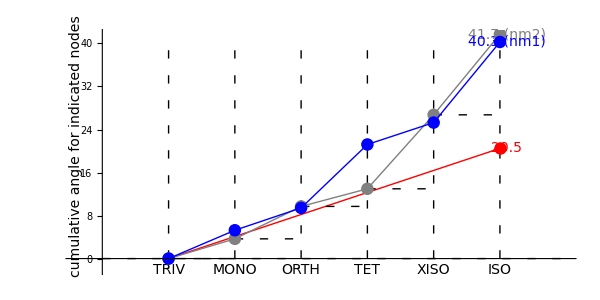

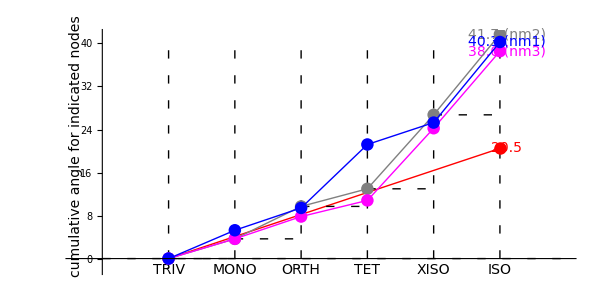

#### direct, nm1, nm2, nm3 for four different node sequences

-Graphics-

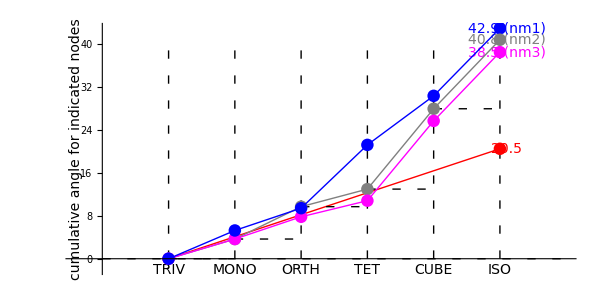

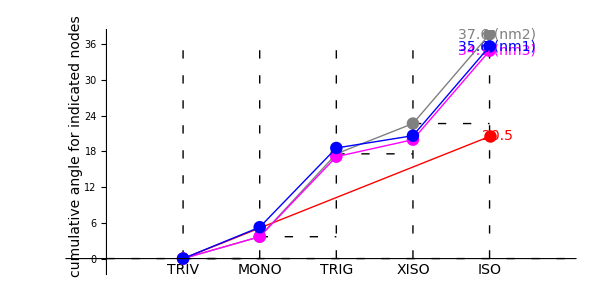

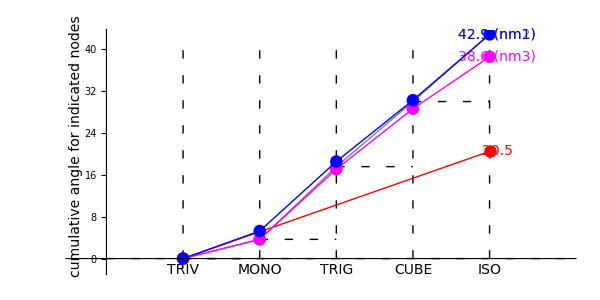

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

## BrownAn48

#### Sequentially add nm1, nm2, nm3 to each plot

12-7-2023 6:21

T is BrownAn48

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.000955066 | -0.994924 | -0.100625
-0.00944278 | -0.100629 | 0.994879
-0.999955 | 0. | -0.00949095)

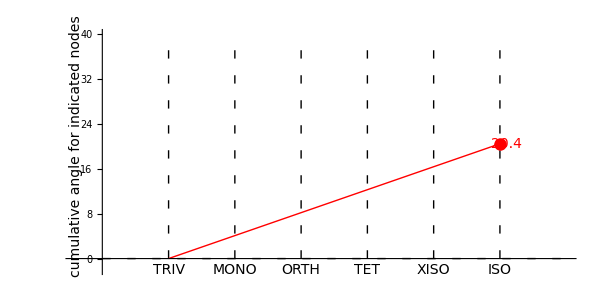

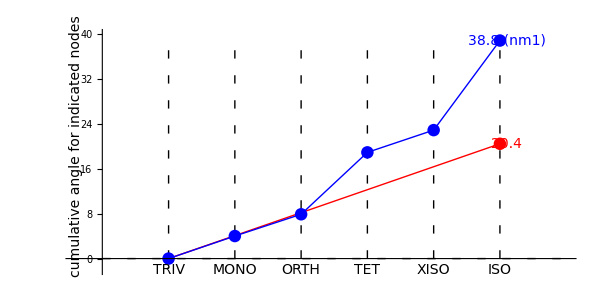

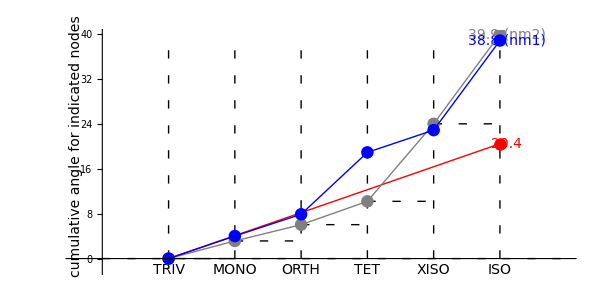

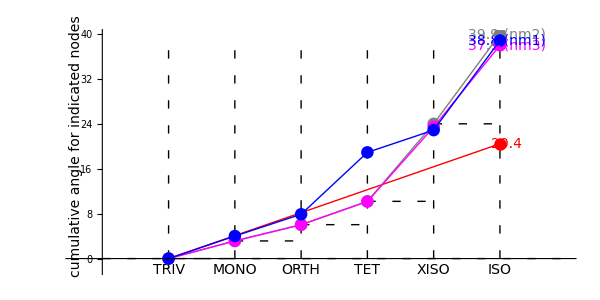

#### direct, nm1, nm2, nm3 for four different node sequences

-Graphics-

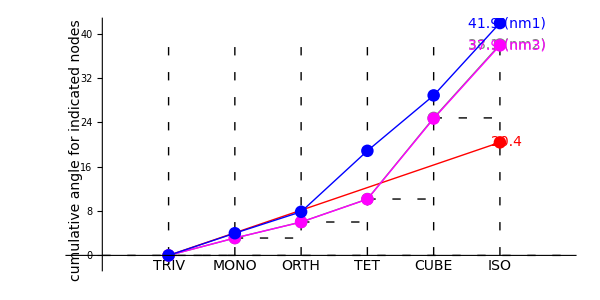

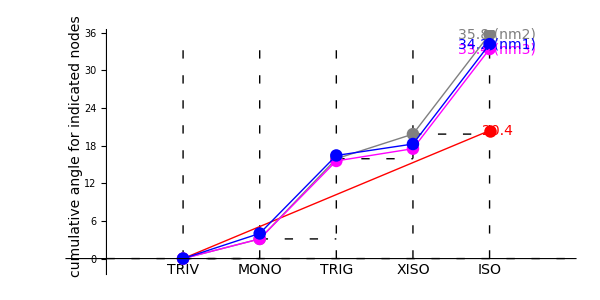

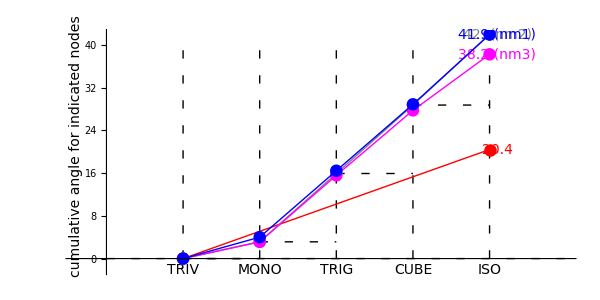

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

## BrownAn60

#### Sequentially add nm1, nm2, nm3 to each plot

12-7-2023 6:39

T is BrownAn60

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.00221262 | -0.997378 | -0.0723372
-0.0304931 | -0.0723711 | 0.996912
-0.999533 | 0. | -0.0305733)

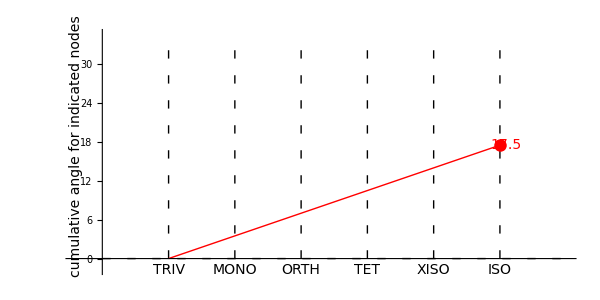

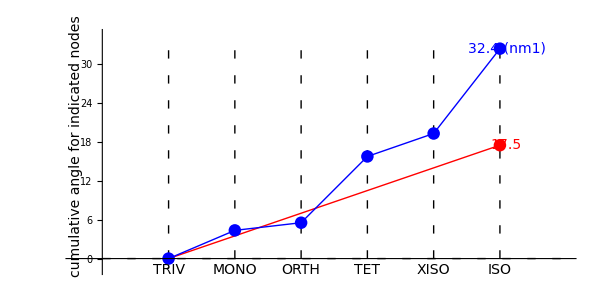

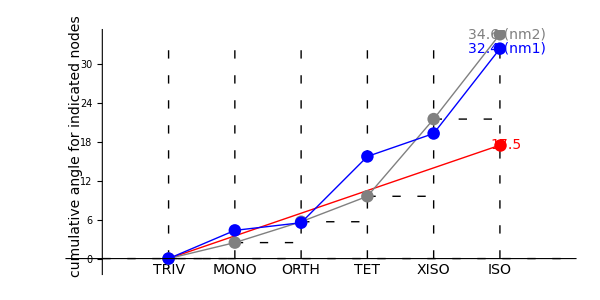

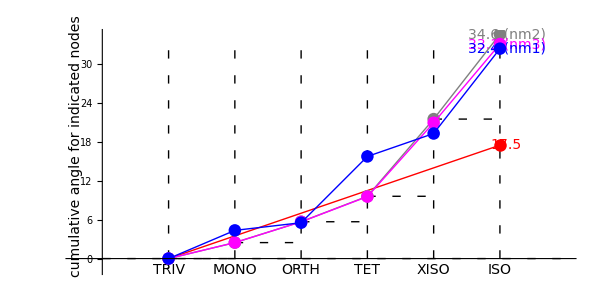

#### direct, nm1, nm2, nm3 for four different node sequences

-Graphics-

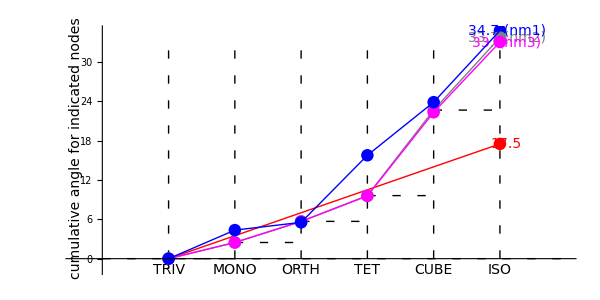

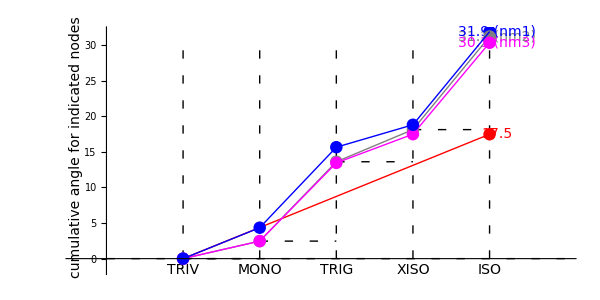

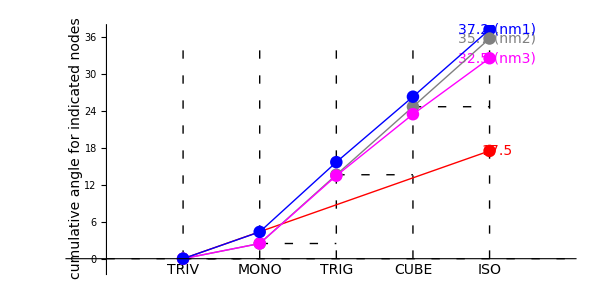

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

## BrownAn78

#### Sequentially add nm1, nm2, nm3 to each plot

12-7-2023 6:56

T is BrownAn78

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.000961598 | -0.993893 | -0.110347
-0.00866079 | -0.110351 | 0.993855
-0.999962 | 0. | -0.00871401)

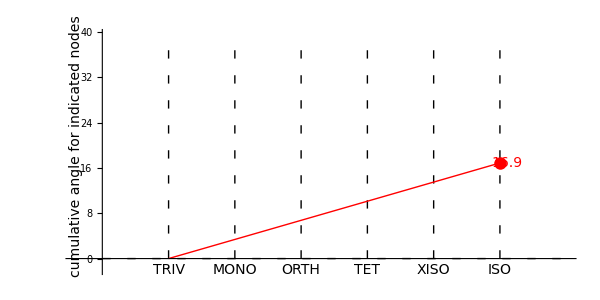

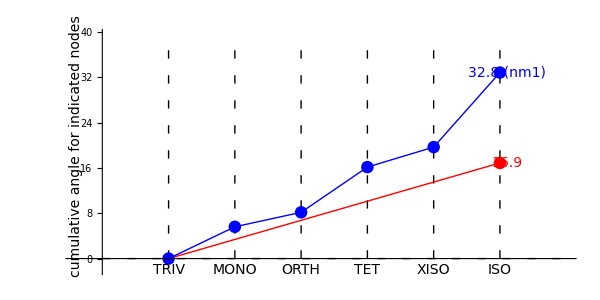

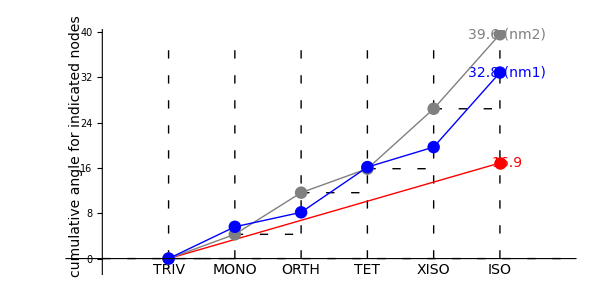

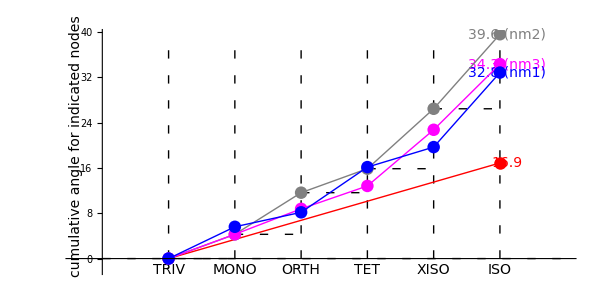

#### direct, nm1, nm2, nm3 for four different node sequences

-Graphics-

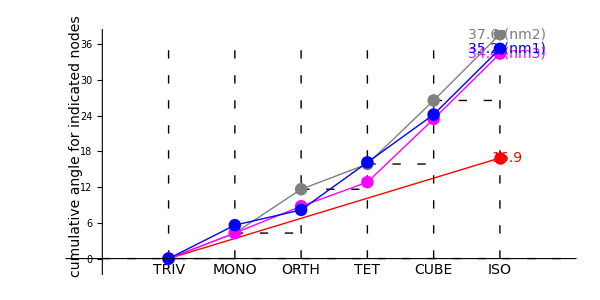

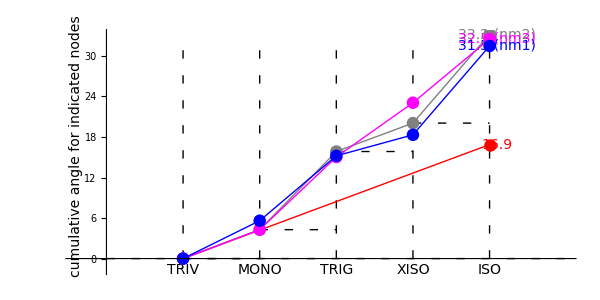

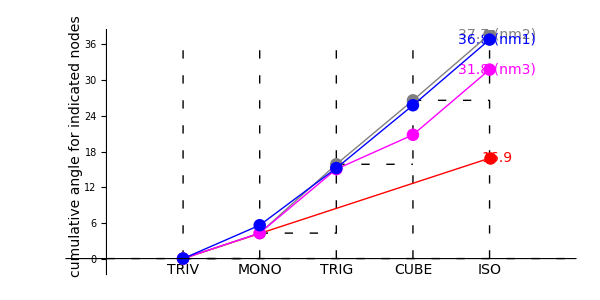

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

## BrownAn96

#### Sequentially add nm1, nm2, nm3 to each plot

12-20-2023 22:36

T is BrownAn96

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (-0.00137287 | -0.997863 | -0.0653337
0.0209636 | -0.0653481 | 0.997642
-0.999779 | 0. | 0.0210085)

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### direct, nm1, nm2, nm3 for four different node sequences

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## Igel

#### Sequentially add nm1, nm2, nm3 to each plot

12-21-2023 9:49

T is Igel

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.0498003 | -0.997825 | 0.0431815
0.753887 | 0.0659144 | 0.65369
-0.655115 | 0. | 0.75553)

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### direct, nm1, nm2, nm3 for four different node sequences

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## SSA2023

#### Sequentially add nm1, nm2, nm3 to each plot

12-21-2023 12:35

T is SSA2023

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.116812 | -0.955654 | 0.270334
0.379065 | 0.294492 | 0.87726
-0.917968 | 0. | 0.396655)

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### direct, nm1, nm2, nm3 for four different node sequences

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## Mar17

#### Sequentially add nm1, nm2, nm3 to each plot

12-21-2023 21:26

T is Mar17

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.261187 | -0.95316 | 0.152536
0.823076 | 0.302466 | 0.480686
-0.504308 | 0. | 0.863524)

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### direct, nm1, nm2, nm3 for four different node sequences

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-